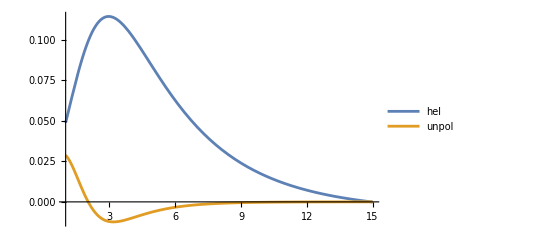

```mathematica
p = 5;
Qeff = 3;
Clear[r]
Plot[{NIntegrate[r p r BesselJ[0, p r]  BesselK[0, Qeff r] Log[1/r^2], {r,10^-5, 10}],NIntegrate[r p r  BesselK[0, Qeff r] BesselJ[0, p r] r^2, {r,10^-5, 10}]}, {p,1,15}, PlotLegends->{"hel", "unpol"}]
```

```mathematica
Solve[Sqrt[3/(2π)] Log[1/p^2] == 15, p]//N
```

{{p→-0.0000193268},{p→0.0000193268}}

```mathematica
100 - 68
```

32

```mathematica
(100 - 65)/2.
```

17.5

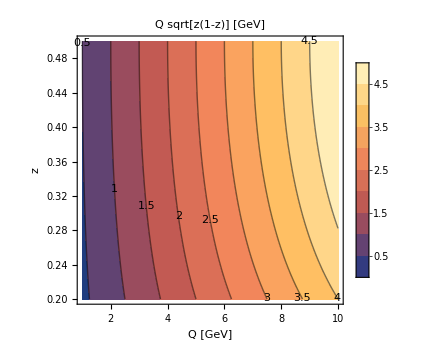

```mathematica
ContourPlot[Q Sqrt[z(1-z)], {Q,1,10}, {z, 0.2, 0.5},
PlotLegends->Automatic,
FrameLabel->{Style[Text["Q [GeV]"],FontSize->16,FontFamily->"Times"],Style[Text["z"],FontSize->16,FontFamily->"Times"]}, ContourLabels->True, 
PlotLabel->Style[Text["Q sqrt[z(1-z)]  [GeV]"],FontSize->16,FontFamily->"Times"],
ImageSize->Medium]
```

```mathematica
10*Sqrt[0.4*0.6]
```

4.89898